```mathematica
(* Load the data. Notice that in our expression we use Pk rather than Tk *)
ClearAll;
CAMBPkFile="Pk_matter_z_0.txt";
DataInput = Import[FileNameJoin[{NotebookDirectory[],CAMBPkFile}], "Table"];

PkData = DataInput[[All,2]];
kData=DataInput[[All,1]];

kMin=Min[kData];
kMax=Max[kData];

(* Set relevant cosmological parameters and functions *)
H0=68;
Omegam0=0.311;
SpeedOfLight=3*10^5;

Hubble[z_]:=H0*Sqrt[Omegam0*(1+z)^3+1-Omegam0]
Omegama[z_]:=Omegam0*(1+z)^3/(Hubble[z]/H0)^2
GrowthRatef[z_]:=Omegama[z]^(6/11)

(* Overall amplitude factor of the B power spectrum*)
AmpDeltaB=9.0/2.0*Omegam0^2*H0^4*Hubble[0]^2*GrowthRatef[0]^2/SpeedOfLight^6;

(* Interpolate data for convenient integration *)
PkInter=Interpolation[DataInput];

(* Impose sensible cutoff if trying to match simulation results. Also avoids extrapolation. *)
(*kminCutoff=kMin;
kmaxCutoff=kMax;*)
kminCutoff=0.01;
kmaxCutoff=12;
(*kminCutoff=0.8*(2*Pi/256);
kmaxCutoff=N[Pi*1024/256];*)

Pk[k_]:=Piecewise[{{PkInter[k],kminCutoff<=k<=kmaxCutoff}},0];

(* Define the dimensionless power spectrum Δ for each field. *)

(* Matter overdensity *)
DeltaMat[k_]:=k^3/(2π^2)*Pk[k];

(* Velocity potential *)
DeltaVel[k_]:=k^3/(2π^2)*Pk[k]/k^4;

(* Cross spectrum *)
DeltaMxV[k_]:=k^3/(2π^2)*Pk[k]/k^2;

(* Define the integration kernels and double integral for the ΔB calculation *)
PIKernel[u_,w_]:=1/u^2*1/w^4*(4w^2-(1+w^2-u^2)^2);
DeltaCombination[k_,u_,w_]:=DeltaMat[k*u] *DeltaVel[k*w]-w/u*DeltaMxV[k*u] *DeltaMxV[k*w];

Idu[k_,w_?NumericQ]:=NIntegrate[PIKernel[u,w]*DeltaCombination[k,u,w],{u,Evaluate[Abs[1-w]], 1+w},Method->"LocalAdaptive"];
Idw[k_]:=NIntegrate[Idu[k,w],{w,0,Infinity}, Method->"LocalAdaptive"];

DeltaB[k_]:=1/k^2*Idw[k];
```

```mathematica
(* Now evaluate all to calculate Δ_BB for a list of k-modes *)
LogRange[xmin_,xmax_,numPoints_]:=Exp[Range[Log[xmin],Log[xmax],(Log[xmax]-Log[xmin])/(numPoints-1)]];

kOutput=LogRange[0.01, 10, 10];
DeltaBOut={};

Table[
ResultInt = DeltaB[k];
AppendTo[DeltaBOut,ResultInt*AmpDeltaB];
,{k,kOutput}];

(* Print results *)
kOutput
DeltaBOut
```

{0.01,0.0215443,0.0464159,0.1,0.215443,0.464159,1.,2.15443,4.64159,10.}

{1.60464×10^-17,8.00713×10^-17,1.81742×10^-16,2.02445×10^-16,1.39683×10^-16,6.77657×10^-17,2.70277×10^-17,9.44228×10^-18,3.00792×10^-18,8.963×10^-19}

Debugging  and Testing Area

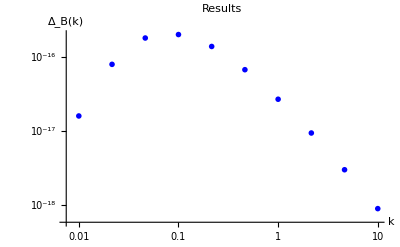

```mathematica
(* Plot results *)
plotData=Transpose[{kOutput,DeltaBOut}];
plotPB=ListLogLogPlot[plotData,PlotStyle->{Blue,PointSize[0.01]},AxesLabel->{"k","Δ_B(k)"},PlotLabel->"Results",GridLines->Automatic]
```

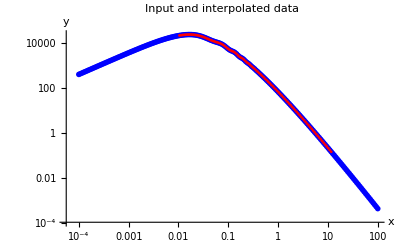

```mathematica
(* Plot Input and interpolated Pk *)
plotDataInput=Transpose[{kData,PkData}];
plotDataInter=Transpose[{kData,Pk/@kData}];
plotInput=ListLogLogPlot[plotDataInput,PlotStyle->{Blue,PointSize[0.01]},AxesLabel->{"k","P(k)"},PlotLabel->"Results",GridLines->Automatic,DataRange->{0.01,0.05}];
plotInter=ListLogLogPlot[plotDataInter,PlotStyle->{Red,PointSize[0.005]},AxesLabel->{"k","P(k)"},PlotLabel->"Results",GridLines->Automatic,DataRange->{0.01,0.05}];

combinedPlot=Show[plotInput,plotInter,PlotLegends->{"Input","Interpolated"},AxesLabel->{"x","y"},PlotLabel->"Input and interpolated data"]
```

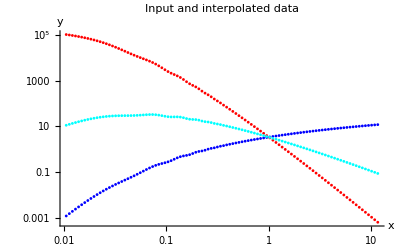

```mathematica
(* Plot the Δ used for the final integral *)
plotDeltaMat=Transpose[{kData,DeltaMat/@kData}];
plotDeltaVel=Transpose[{kData,DeltaVel/@kData}];
plotDeltaMxV=Transpose[{kData,DeltaMxV/@kData}];

plotDeltaMat=ListLogLogPlot[plotDeltaMat,PlotStyle->{Blue,PointSize[0.005]},AxesLabel->{"k","P(k)"},PlotLabel->"Results",GridLines->Automatic,DataRange->Automatic];
plotDeltaVel=ListLogLogPlot[plotDeltaVel,PlotStyle->{Red,PointSize[0.005]},AxesLabel->{"k","P(k)"},PlotLabel->"Results",GridLines->Automatic,DataRange->Automatic];
plotDeltaMxV=ListLogLogPlot[plotDeltaMxV,PlotStyle->{Cyan,PointSize[0.005]},AxesLabel->{"k","P(k)"},PlotLabel->"Results",GridLines->Automatic,DataRange->Automatic];

Show[plotDeltaMat,plotDeltaVel,plotDeltaMxV,PlotRange->Automatic,PlotLegends->{"Input","Interpolated"},AxesLabel->{"x","y"},PlotLabel->"Input and interpolated data"]
```

```mathematica
(* Plot against old data. Apparently this is not the paper's one but seems to have the correct shape. *)
TestkBFile="old_results/kbb_vector_z05_cutoffs2_L256_PM1024.dat";TestPBFile="old_results/Pbb_vector_z05_cutoffs2_L256_PM1024.dat";
TestkB = Flatten[Import[FileNameJoin[{NotebookDirectory[],TestkBFile}], "Table"]];
TestPB = Flatten[Import[FileNameJoin[{NotebookDirectory[],TestPBFile}], "Table"]];
```

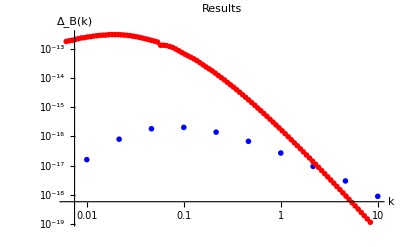

```mathematica
plotTestData=Transpose[{TestkB,TestPB}];
plotTest=ListLogLogPlot[plotTestData,PlotStyle->{Red,PointSize[0.01]},AxesLabel->{"k","Δ_B(k)"},PlotLabel->"Results",GridLines->Automatic];

Show[plotPB,plotTest,PlotRange->Automatic]
```